#### Качественный анализ двумерной модели конкуренции

```mathematica
G = {Subscript[a, 1] Subscript[x, 1]-Subscript[b, 12] Subscript[x, 1] Subscript[x, 2]-Subscript[c, 1] Subscript[x, 1]^2,
Subscript[a, 2] Subscript[x, 2]-Subscript[b, 21] Subscript[x, 1] Subscript[x, 2]-Subscript[c, 2] Subscript[x, 2]^2};
```

```mathematica
points=Solve[G==0,{Subscript[x, 1],Subscript[x, 2]}]
```

{{x_1→0,x_2→0},{x_1→0,x_2→a_2/c_2},{x_1→-(-a_2 b_12+a_1 c_2)/(b_12 b_21-c_1 c_2),x_2→-(a_1 b_21-a_2 c_1)/(-b_12 b_21+c_1 c_2)},{x_1→a_1/c_1,x_2→0}}

```mathematica
A=Grad[G,{Subscript[x, 1],Subscript[x, 2]}];
A //MatrixForm
```

(a_1-2 c_1 x_1-b_12 x_2 | -b_12 x_1
-b_21 x_2 | a_2-b_21 x_1-2 c_2 x_2)

```mathematica
Subscript[A, 1]=A/.{Subscript[x, 1]->0,Subscript[x, 2]->0};
```

```mathematica
Eigenvalues@Subscript[A, 1]
```

{a_1,a_2}

```mathematica
Eigenvectors@Subscript[A, 1]
```

{{1,0},{0,1}}

Вывод:  - неустойчивый узел

```mathematica
Subscript[A, 2]=A/.{Subscript[x, 1]->Subscript[a, 1]/Subscript[c, 1],Subscript[x, 2]->0};
```

```mathematica
Eigenvalues@Subscript[A, 2]
```

{-a_1,(-a_1 b_21+a_2 c_1)/c_1}

```mathematica
Eigenvectors@Subscript[A, 2]
```

{{1,0},{(a_1 b_12)/(a_1 b_21-a_1 c_1-a_2 c_1),1}}

Вывод:  - устойчивый узел при  (1)
			- седло при  (2)

```mathematica
Subscript[A, 3]=A/.{Subscript[x, 1]->0,Subscript[x, 2]->Subscript[a, 2]/Subscript[c, 2]};
```

```mathematica
Eigenvalues@Subscript[A, 3]
```

{-a_2,(-a_2 b_12+a_1 c_2)/c_2}

```mathematica
Eigenvectors@Subscript[A, 3]
```

{{0,1},{-(-a_2 b_12+a_1 c_2+a_2 c_2)/(a_2 b_21),1}}

Вывод:  - устойчивый узел при  (3)
			- седло при  (4)

```mathematica
Subscript[A, 4]=A/.{Subscript[x, 1]->(Subscript[a, 2] Subscript[b, 12]-Subscript[a, 1] Subscript[c, 2])/(Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2]),Subscript[x, 2]->(Subscript[a, 1] Subscript[b, 21]-Subscript[a, 2] Subscript[c, 1])/(Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2])};
```

При каких условиях ?
(I): 	(3) ∧ (1), т. к. (3) * (1) =>  
(II):	(4) ∧ (2), т. к. (4) * (2) =>

```mathematica
det=Simplify@Det@Subscript[A, 4]
```

((a_1 b_21-a_2 c_1) (-a_2 b_12+a_1 c_2))/(b_12 b_21-c_1 c_2)

(I):	det A_4 < 0
(II):	det A_4 > 0

```mathematica
trace=Simplify@Tr@Subscript[A, 4]
```

(a_1 (-b_21+c_1) c_2+a_2 c_1 (-b_12+c_2))/(b_12 b_21-c_1 c_2)

trace = (c_1(a_1 c_2-a_2 b_12)+c_2(a_2 c_1-a_1 b_21))/(b_12 b_21-c_1 c_2)

(II):	tr A_4 < 0

```mathematica
Reduce[trace^2-4*det<0 &&
Subscript[a, 1]>0&&Subscript[a, 2]>0&&Subscript[b, 12]>0&&Subscript[b, 21]>0&&Subscript[c, 1]>0 &&Subscript[c, 2]>0&&
Subscript[a, 1] Subscript[b, 21]<Subscript[a, 2] Subscript[c, 1]&&Subscript[a, 2] Subscript[b, 12]<Subscript[a, 1] Subscript[c, 2],
{Subscript[a, 1],Subscript[a, 2],Subscript[b, 12],Subscript[b, 21],Subscript[c, 1], Subscript[c, 2]}]
```

False

```mathematica
Reduce[trace^2-4*det>0 &&
Subscript[a, 1]>0&&Subscript[a, 2]>0&&Subscript[b, 12]>0&&Subscript[b, 21]>0&&Subscript[c, 1]>0 &&Subscript[c, 2]>0&&
Subscript[a, 1] Subscript[b, 21]<Subscript[a, 2] Subscript[c, 1]&&Subscript[a, 2] Subscript[b, 12]<Subscript[a, 1] Subscript[c, 2],
{Subscript[a, 1],Subscript[a, 2],Subscript[b, 12],Subscript[b, 21],Subscript[c, 1], Subscript[c, 2]}]
```

a_1>0&&a_2>0&&b_12>0&&b_21>0&&c_1>(a_1 b_21)/a_2&&c_2>(a_2 b_12)/a_1

(II):	(tr A_4)^2-4det A_4 >0

Вывод:  - седло при  (1) ∧  (3)
							      - устойчивый узел при  (2) ∧  (4)

Итого: (фазовый портрет)
(I):	 
	 - неустойчивый узел
	 - устойчивый узел
	 - устойчивый узел
	 - седло

(II):	
	 - неустойчивый узел
	 - седло
	 - седло
	 - устойчивый узел

```mathematica
streamPlot[G_List,points_List,params_List,arrowSize_Real]:=Module[
{x1max, x2max},
If[
Equal[Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2],0]/.params,
Print["Invalid parameter values"],
x1max =Round@Max[Subscript[a, 1]/Subscript[c, 1],If[(Subscript[a, 2] Subscript[b, 12]-Subscript[a, 1] Subscript[c, 2])/(Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2])*(Subscript[a, 1] Subscript[b, 21]-Subscript[a, 2] Subscript[c, 1])/(Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2])>0,(Subscript[a, 2] Subscript[b, 12]-Subscript[a, 1] Subscript[c, 2])/(Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2]),0]]/.params;
x2max=Round@Max[Subscript[a, 2]/Subscript[c, 2],If[(Subscript[a, 2] Subscript[b, 12]-Subscript[a, 1] Subscript[c, 2])/(Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2])*(Subscript[a, 1] Subscript[b, 21]-Subscript[a, 2] Subscript[c, 1])/(Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2])>0, (Subscript[a, 1] Subscript[b, 21]-Subscript[a, 2] Subscript[c, 1])/(Subscript[b, 12] Subscript[b, 21]-Subscript[c, 1] Subscript[c, 2]),0]]/.params;
StreamPlot[G/.params,
{Subscript[x, 1],0,1.25x1max},{Subscript[x, 2],0,1.25x2max},
Epilog->{Red,Point[(points/.params)⟦All,All,2⟧]},
StreamPoints->Fine,
StreamScale->{Full, All, arrowSize},
StreamColorFunction->"Rainbow",
PerformanceGoal->"Quality"],
Text[params,{0,-1}]
]
]
```

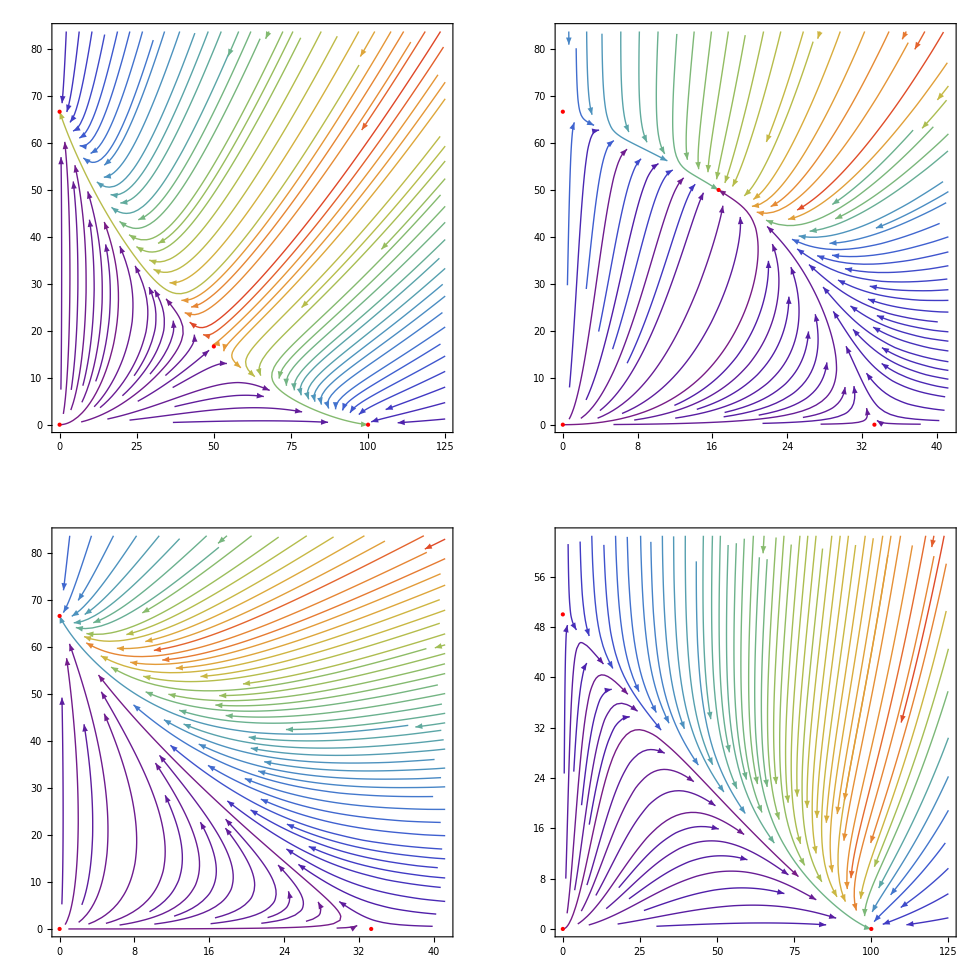

```mathematica
GraphicsGrid[
{
{streamPlot[G,points,{Subscript[a, 1]->10,Subscript[a, 2]->20,Subscript[b, 12]->0.3,Subscript[b, 21]->0.3,Subscript[c, 1]->0.1,Subscript[c, 2]->0.3},.015],
streamPlot[G,points,{Subscript[a, 1]->10,Subscript[a, 2]->20,Subscript[b, 12]->0.1,Subscript[b, 21]->0.3,Subscript[c, 1]->0.3,Subscript[c, 2]->0.3},.007]},

{streamPlot[G,points,{Subscript[a, 1]->10,Subscript[a, 2]->20,Subscript[b, 12]->0.4,Subscript[b, 21]->0.3,Subscript[c, 1]->0.3,Subscript[c, 2]->0.3},.007],
streamPlot[G,points,{Subscript[a, 1]->10,Subscript[a, 2]->20,Subscript[b, 12]->0.1,Subscript[b, 21]->0.3,Subscript[c, 1]->0.1,Subscript[c, 2]->0.4},.015]}
}
]
```

Граничные случаи:   и

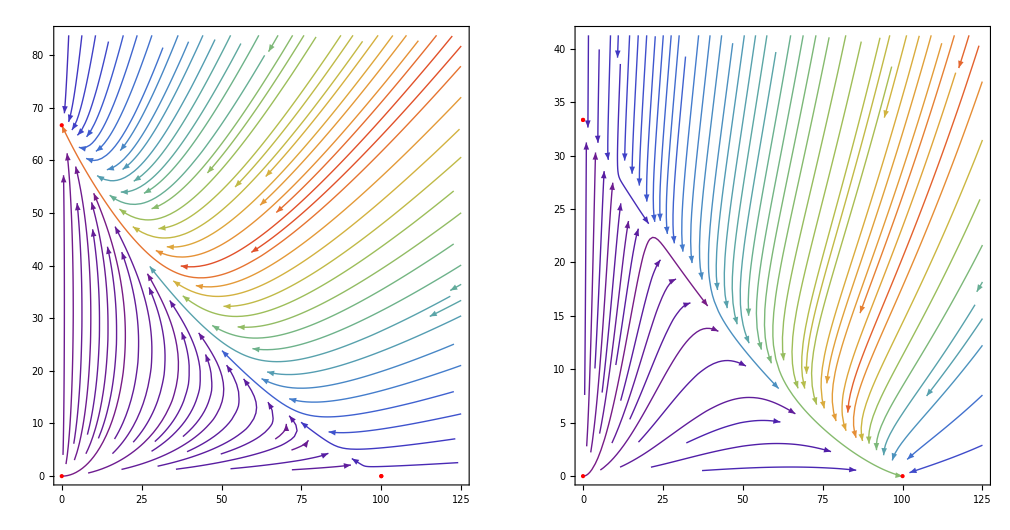

```mathematica
GraphicsGrid[
{{streamPlot[G,points,{Subscript[a, 1]->10,Subscript[a, 2]->20,Subscript[b, 12]->0.3,Subscript[b, 21]->0.2,Subscript[c, 1]->0.1,Subscript[c, 2]->0.3},.015],
streamPlot[G,points,{Subscript[a, 1]->10,Subscript[a, 2]->20,Subscript[b, 12]->0.3,Subscript[b, 21]->0.3,Subscript[c, 1]->0.1,Subscript[c, 2]->0.6},.015]}}
]
```